# Lab 3

## Question 1

### a)

```mathematica
i=3
```

3

```mathematica
x[i_]:=(
Binomial[3,2]*Binomial[17,i-3]/Binomial[20,i-1]*(1/(20-i+1))
)
```

```mathematica
N[x[i],5]
```

0.00087719

### b)

```mathematica
i=4;
```

```mathematica
x[i]
```

1/380

### c)

```mathematica
i=Range[3,20,2];
Total[x[i]]
```

35/76

```mathematica
Sum[x[i],{i,3,20,2}]
```

35/76

### d)

```mathematica
Sum[x[i],{i,4,20,2}]
```

41/76

## Question 2

### a)

```mathematica
f[x_]:=(
Binomial [20,x]*Binomial[100-20,5-x]/Binomial[100,5]
)
```

### b)

```mathematica
x=0;
N[f[x],7]
```

0.3193094

### c)

```mathematica
N[Sum[f[x],{x,0,3}],7]
```

0.9946458

```mathematica
Sum[f[x],{x,0,5}]
```

1

### d)

```mathematica
e[x_]:=(
Total[x*f[x]]
)
```

```mathematica
x=Range[0,5];
```

```mathematica
e[x]
```

1

### e)

```mathematica
Total[x^2*f[x]]
```

175/99

### f)

```mathematica
Var[x_]:=(
Total[x^2*f[x]]-(e[x])^2
)
```

```mathematica
N[Var[x],7]
```

0.7676768

### g)

```mathematica
{x,f[x]}
```

{{0,1,2,3,4,5},{19513/61110,5135/12222,97565/470547,7505/156849,1615/313698,323/1568490}}

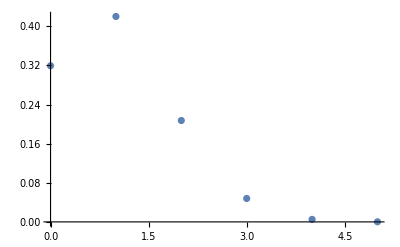

```mathematica
ListPlot[Transpose[{x,f[x]}]]
```

```mathematica
ListPlot[Thread[{x,f[x]}]]
```

-Graphics-